```mathematica
SetDirectory[NotebookDirectory[]];
```

## Use discretized data

```mathematica
axis=Import["data/output/x_axis.txt","Data"]//Flatten;
Tq10=Import["data/output/Tq_value_mu_10.0.txt","Data"]//Flatten;
Tq1000=Import["data/output/Tq_value_mu_1000.0.txt","Data"]//Flatten;
Tg10=Import["data/output/Tg_value_mu_10.0.txt","Data"]//Flatten;
Tg1000=Import["data/output/Tg_value_mu_1000.0.txt","Data"]//Flatten;
```

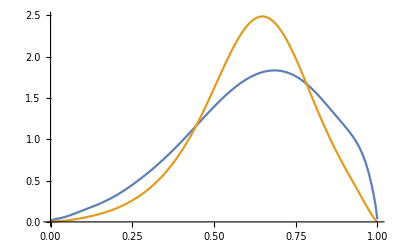

```mathematica
{Transpose[{axis,Tq10}],Transpose[{axis,Tq1000}]}//ListLinePlot
```

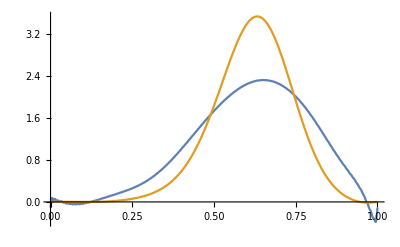

```mathematica
{Transpose[{axis,Tg10}],Transpose[{axis,Tg1000}]}//ListLinePlot
```

## Use coefficients

```mathematica
import[file_String]:=Total/@(Import[file,"Data"]/.{a_,b_String,c_String}:> {a,StringJoin[b,c]//StringReplace[#,{"e-"~~x_:> "*10^(-"~~x~~")","im"-> "*I"}]&//ToExpression})
```

```mathematica
mu$10$data=import["data/output/NLO_fourier_coeff_mu_10.0.txt"];
quark$10GeV[x_]:=quark$10GeV[x]=1+2Re[mu$10$data[[1;;100]].Table[Exp[2Pi I n x],{n,1,100}]]
gluon$10GeV[x_]:=gluon$10GeV[x]=1+2Re[mu$10$data[[101;;200]].Table[Exp[2Pi I n x],{n,1,100}]]
```

```mathematica
mu$1000$data=import["data/output/NLO_fourier_coeff_mu_1000.0.txt"];
quark$1000GeV[x_]:=quark$1000GeV[x]=1+2Re[mu$1000$data[[1;;100]].Table[Exp[2Pi I n x],{n,1,100}]]
gluon$1000GeV[x_]:=gluon$1000GeV[x]=1+2Re[mu$1000$data[[101;;200]].Table[Exp[2Pi I n x],{n,1,100}]]
```

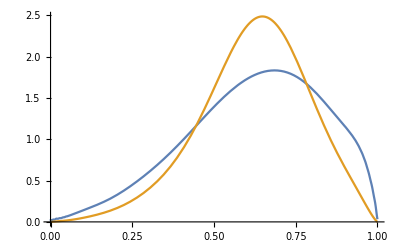

```mathematica
Plot[{quark$10GeV[x],quark$1000GeV[x]},{x,0,1}]
```

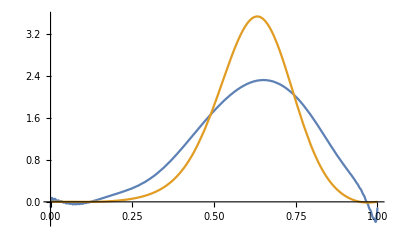

```mathematica
Plot[{gluon$10GeV[x],gluon$1000GeV[x]},{x,0,1}]
```